Задание №2
Изобразить на рисунке обл. плоскости Z, поеределяемую заданными неравенствами.
|z-2|<1
Re(z) > 1.5
Im(z)≥ -0.5

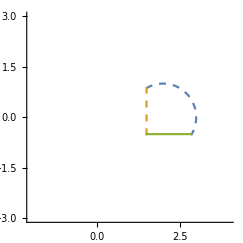

```mathematica
ContourPlot[{(x-2)^2+y^2==1,x==1.5,y==-0.5},{x,-2,4},{y,-3,3},ContourStyle->{Dashed,Dashed,Thickness[2]},RegionFunction->Function[{x,y},(x-2)^2+y^2<1 && x≥ 1.5 && y≥-0.5],Frame->False,Axes->True]
```

Функция ContourPlot строит графики 3 функций на произвольном промежутке, 
RegionFunction это опция которую принимает функция  ContourPlot которая ограничивает область на которой строятся эти графики.

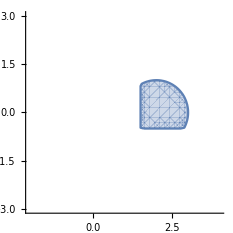

```mathematica
RegionPlot[(x-2)^2+y^2<1 && x≥ 1.5 && y≥-0.5,{x,-2,4},{y,-3,3},Frame->False,Axes->True]
```

Функция RegionPlot просто строит область.